{5-8 p+8 p^2,5-8 p+9 p^2-p^3,5-8 p+9 p^2-2 p^4,5-7 p+8 p^2-p^3,5-7 p+8 p^2-2 p^4,5-7 p+9 p^2-2 p^3-2 p^4,5-7 p+6 p^2+p^3,5-7 p+7 p^2,5-7 p+7 p^2+p^3-2 p^4,5-6 p+6 p^2,5-6 p+6 p^2+p^3-2 p^4,5-6 p+7 p^2-p^3-2 p^4,4-2 p-3 p^2+8 p^3-2 p^4,4-2 p-2 p^2+7 p^3-2 p^4,4-2 p-2 p^2+8 p^3-4 p^4,4-p-3 p^2+7 p^3-2 p^4,4-p-3 p^2+8 p^3-4 p^4,4-p-2 p^2+6 p^3-4 p^4,5-6 p+5 p^2+p^3,5-5 p+5 p^2,5-5 p+5 p^2+p^3-2 p^4,5-5 p+6 p^2-p^3-2 p^4,4-p-4 p^2+8 p^3-2 p^4,4-4 p^2+7 p^3-2 p^4,4-4 p^2+8 p^3-4 p^4,4-3 p^2+6 p^3-4 p^4,3+3 p-9 p^2+10 p^3-2 p^4,3+3 p-8 p^2+9 p^3-2 p^4,3+3 p-8 p^2+10 p^3-4 p^4,3+4 p-9 p^2+9 p^3-2 p^4,3+4 p-9 p^2+10 p^3-4 p^4,3+4 p-8 p^2+8 p^3-4 p^4,5-5 p+5 p^2-p^3-2 p^4,4-4 p^2+6 p^3-4 p^4,3+4 p-9 p^2+8 p^3-4 p^4,2+6 p-10 p^2+9 p^3-2 p^4,2+6 p-10 p^2+10 p^3-4 p^4,2+6 p-9 p^2+8 p^3-4 p^4,2+6 p-10 p^2+8 p^3-4 p^4}

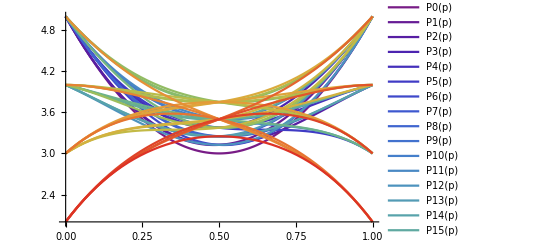

Piecewise[{{5-8 p+8 p^2, Root0.356Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,1]0.3561576120381933≤p≤Root0.644Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,2]0.6438423879618067}, {-2 (-1-3 p+5 p^2-4 p^3+2 p^4), True}}]

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.16553,{p→0.356158}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.16553,{p→0.643842}}

1.19836

-2.30148

{{p→Root0.356Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,1]0.3561576120381933},{p→Root0.644Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,2]0.6438423879618067}}

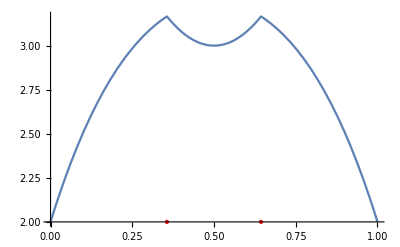

```mathematica
P0[p_]=5p^0+-8p^1+8p^2+0p^3+0p^4+0p^5;
P1[p_]=5p^0+-8p^1+9p^2+-1p^3+0p^4+0p^5;
P2[p_]=5p^0+-8p^1+9p^2+0p^3+-2p^4+0p^5;
P3[p_]=5p^0+-7p^1+8p^2+-1p^3+0p^4+0p^5;
P4[p_]=5p^0+-7p^1+8p^2+0p^3+-2p^4+0p^5;
P5[p_]=5p^0+-7p^1+9p^2+-2p^3+-2p^4+0p^5;
P6[p_]=5p^0+-7p^1+6p^2+1p^3+0p^4+0p^5;
P7[p_]=5p^0+-7p^1+7p^2+0p^3+0p^4+0p^5;
P8[p_]=5p^0+-7p^1+7p^2+1p^3+-2p^4+0p^5;
P9[p_]=5p^0+-6p^1+6p^2+0p^3+0p^4+0p^5;
P10[p_]=5p^0+-6p^1+6p^2+1p^3+-2p^4+0p^5;
P11[p_]=5p^0+-6p^1+7p^2+-1p^3+-2p^4+0p^5;
P12[p_]=4p^0+-2p^1+-3p^2+8p^3+-2p^4+0p^5;
P13[p_]=4p^0+-2p^1+-2p^2+7p^3+-2p^4+0p^5;
P14[p_]=4p^0+-2p^1+-2p^2+8p^3+-4p^4+0p^5;
P15[p_]=4p^0+-1p^1+-3p^2+7p^3+-2p^4+0p^5;
P16[p_]=4p^0+-1p^1+-3p^2+8p^3+-4p^4+0p^5;
P17[p_]=4p^0+-1p^1+-2p^2+6p^3+-4p^4+0p^5;
P18[p_]=5p^0+-6p^1+5p^2+1p^3+0p^4+0p^5;
P19[p_]=5p^0+-5p^1+5p^2+0p^3+0p^4+0p^5;
P20[p_]=5p^0+-5p^1+5p^2+1p^3+-2p^4+0p^5;
P21[p_]=5p^0+-5p^1+6p^2+-1p^3+-2p^4+0p^5;
P22[p_]=4p^0+-1p^1+-4p^2+8p^3+-2p^4+0p^5;
P23[p_]=4p^0+0p^1+-4p^2+7p^3+-2p^4+0p^5;
P24[p_]=4p^0+0p^1+-4p^2+8p^3+-4p^4+0p^5;
P25[p_]=4p^0+0p^1+-3p^2+6p^3+-4p^4+0p^5;
P26[p_]=3p^0+3p^1+-9p^2+10p^3+-2p^4+0p^5;
P27[p_]=3p^0+3p^1+-8p^2+9p^3+-2p^4+0p^5;
P28[p_]=3p^0+3p^1+-8p^2+10p^3+-4p^4+0p^5;
P29[p_]=3p^0+4p^1+-9p^2+9p^3+-2p^4+0p^5;
P30[p_]=3p^0+4p^1+-9p^2+10p^3+-4p^4+0p^5;
P31[p_]=3p^0+4p^1+-8p^2+8p^3+-4p^4+0p^5;
P32[p_]=5p^0+-5p^1+5p^2+-1p^3+-2p^4+0p^5;
P33[p_]=4p^0+0p^1+-4p^2+6p^3+-4p^4+0p^5;
P34[p_]=3p^0+4p^1+-9p^2+8p^3+-4p^4+0p^5;
P35[p_]=2p^0+6p^1+-10p^2+9p^3+-2p^4+0p^5;
P36[p_]=2p^0+6p^1+-10p^2+10p^3+-4p^4+0p^5;
P37[p_]=2p^0+6p^1+-9p^2+8p^3+-4p^4+0p^5;
P38[p_]=2p^0+6p^1+-10p^2+8p^3+-4p^4+0p^5;

d = {P0[p],P1[p],P2[p],P3[p],P4[p],P5[p],P6[p],P7[p],P8[p],P9[p],
P10[p],P11[p],P12[p],P13[p],P14[p],P15[p],P16[p],P17[p],P18[p],P19[p],
P20[p],P21[p],P22[p],P23[p],P24[p],P25[p],P26[p],P27[p],P28[p],P29[p],
P30[p],P31[p],P32[p],P33[p],P34[p],P35[p],P36[p],P37[p],P38[p]}
Plot[{P0[p],P1[p],P2[p],P3[p],P4[p],P5[p],P6[p],P7[p],P8[p],P9[p],
P10[p],P11[p],P12[p],P13[p],P14[p],P15[p],P16[p],P17[p],P18[p],P19[p],
P20[p],P21[p],P22[p],P23[p],P24[p],P25[p],P26[p],P27[p],P28[p],P29[p],
P30[p],P31[p],P32[p],P33[p],P34[p],P35[p],P36[p],P37[p],P38[p]},{p,0,1},Axes ->True,PlotLegends->"Expressions",PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@d]/Length@d)]

f[p_]=Expand[PiecewiseExpand[FullSimplify[Min[d],0<p<1]]]
{max1,pmax1} = FindMaximum[f[p],{p,0.4}]
{max2,pmax2} = FindMaximum[f[p],{p,0.6}]
Limit[f'[p],p->{p/.pmax1},Direction->"FromBelow"]
Limit[f'[p],p->{p/.pmax1}+0.0000000001,Direction->"FromAbove"]
Solve[FunctionSingularities[f[p],p,Reals]&&0<p<1,p,Reals]
Plot[f[p],{p,0,1},PlotLegends->"Expressions",Epilog->{PointSize[Medium],Red,Point[{p,2}]/. %}]
```

Probabilities of bits being the same

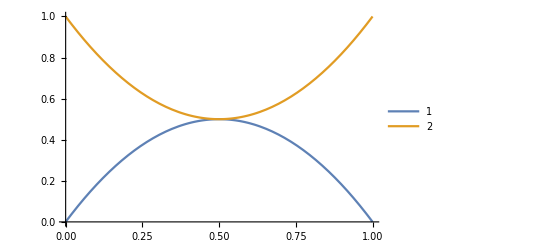

{{p→1/2},{p→1/2}}

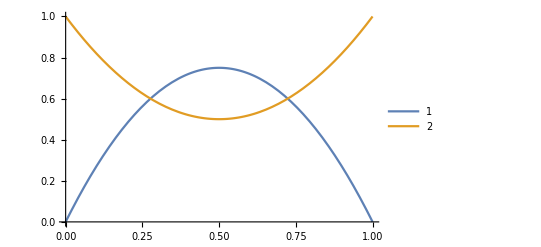

{{p→1/10 (5-√5)},{p→1/10 (5+√5)}}

```mathematica
Plot[{2p(1-p),p^2+(1-p)^2},{p,0,1},PlotLegends->Automatic]
Solve[2p(1-p)==p^2+(1-p)^2&&0<p<1,p,Reals]
Plot[{1-p^3-(1-p)^3,p^2+(1-p)^2},{p,0,1},PlotLegends->Automatic]
Solve[(1-p^3-(1-p)^3)==p^2+(1-p)^2&&0<p<1,p,Reals]
```

```mathematica
N[{{p->1/10 (5-√5)},{p->1/10 (5+√5)}}]
```

{{p→0.276393},{p→0.723607}}